```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Software\\DJS_TEST_AREA\\RF Condition"];
```

```mathematica
traces=Rest[Import["breakdown_trace.txt","Table"]];
```

```mathematica
time=Import["LRF_time_vector.txt","Table"][[1,3;;-1]];
```

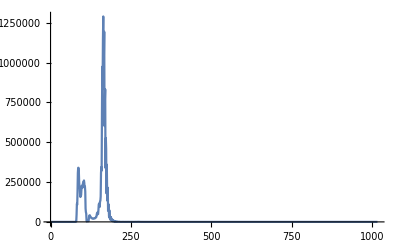

```mathematica
ListLinePlot[Rest[traces[[2]]],PlotRange->All]
```

```mathematica
pos=Min[Position[#,_?(#>200&)][[2,1]]&/@traces]
```

78

```mathematica
actualtraces=Map[Drop[#,pos]&,traces];
```

```mathematica
Length[actualtraces[[1]]]
```

940

```mathematica
modtime=Drop[time,-pos+1];
```

```mathematica
Length[modtime]
```

940

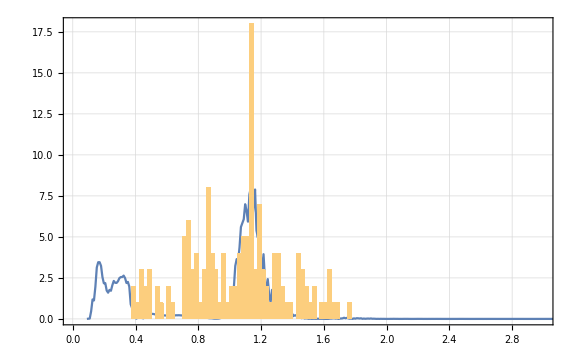

```mathematica
Show[ListLinePlot[{Map[{1,0.00001}#&,Transpose[{modtime,actualtraces[[20]]}]]},PlotRange->All,PlotTheme->"Detailed"],
Histogram[Map[modtime[[Position[#,Max[#]][[1,1]]]]&,actualtraces],{0.0,4,0.025},ImageSize->Large],PlotRange->{{0,3},All},Frame->True
]
```

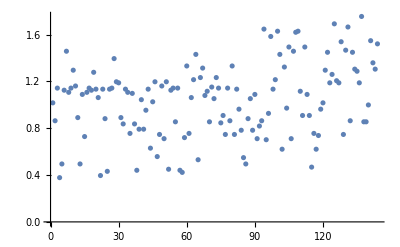

```mathematica
ListPlot[Map[modtime[[Position[#,Max[#]][[1,1]]]]&,actualtraces]]
```

```mathematica
sortedtraces=Sort[actualtraces,Position[#1,Max[#1]][[1,1]]>Position[#2,Max[#2]][[1,1]]&];
```

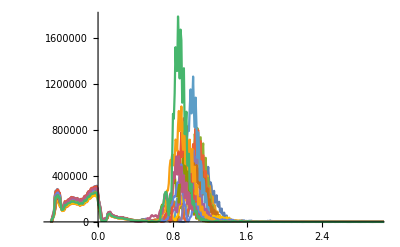

```mathematica
ListLinePlot[Transpose[{modtime-0.6,#}]&/@sortedtraces[[1;;15]],PlotRange->{{All,3},All}]
```

## Probes

```mathematica
SetDirectory["\\\\fed.cclrc.ac.uk\\Org\\NLab\\ASTeC\\Projects\\VELA\\Software\\DJS_TEST_AREA\\RF Condition"];
```

```mathematica
probetraces=Rest[Import["breakdown_trace_probe.txt","Table"]];
```

```mathematica
time=Import["LRF_time_vector.txt","Table"][[1,3;;-1]];
```

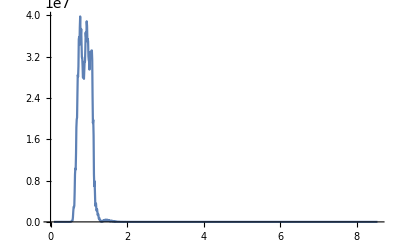

```mathematica
ListLinePlot[Transpose[{modtime,Drop[Rest[probetraces][[2]],pos]}],PlotRange->All]
```

```mathematica
TwoAxisPlot[{f_,g_},opts___]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},
{fgraph,ggraph}=MapIndexed[ListLinePlot[#,Axes->True,opts,PlotRange->All,PlotTheme->"Detailed"]&,{{f,{0}},{{0},g}}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,10];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[97]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

```mathematica
Manipulate[
testtime=probetraces[[$probetrace,1]];
revpos=Position[traces[[All,1]],Nearest[traces[[All,1]],testtime][[1]]][[1,1]];
Show[TwoAxisPlot[
{Transpose[{modtime,1/(2 10^6)Drop[probetraces[[$probetrace]],pos]}],
Transpose[{modtime,1/10^6 actualtraces[[revpos]]}]},PlotRange->{{0,2},All}],Frame->True,ImageSize->800,FrameLabel->{"S [m]","CAV PROBE PWR",None,"CAV REV PWR"},BaseStyle->{FontSize->18},GridLines->{Automatic,Range[0,50,1]}],
{{$probetrace,1},1,Length[probetraces],1}
]
```